```mathematica
(*Mathematica*)
```

```mathematica
Clear[t,a,p,aa,bb]
```

```mathematica
(* 5 symbol Pentagon *)
```

```mathematica
n0=5
```

5

```mathematica
(* substitution *)
```

```mathematica
s[1]={3,4,0,0,0,0,0,0}; s[2]={4,5,0,0,0,0,0,0}; s[3]={1,5,0,0,0,0,0,0}; s[4]={1,2,0,0,0,0,0,0,0};s[5]={2,3,0,0,0,0,0,0,0};
```

```mathematica
(* make matrix*)
```

```mathematica
M=Table[Table[Count[s[j],i],{i,1,n0}],{j,1,n0}]
```

{{0,0,1,1,0},{0,0,0,1,1},{1,0,0,0,1},{1,1,0,0,0},{0,1,1,0,0}}

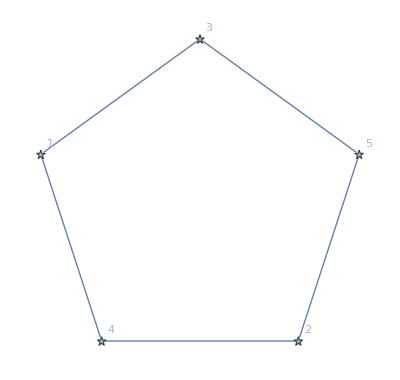

```mathematica
AdjacencyGraph[M,VertexLabels->"Name",ImageSize->Full,VertexShapeFunction->"Star"]
```

```mathematica
(* make polynomial*)
```

```mathematica
Det[M-x*IdentityMatrix[n0]]
```

2-5 x+5 x^3-x^5

```mathematica
x/.NSolve[CharacteristicPolynomial[M,x]==0,x]
```

{-1.61803,-1.61803,0.618034,0.618034,2.}

```mathematica
Abs[%]
```

{1.61803,1.61803,0.618034,0.618034,2.}

```mathematica
Clear[s,p]
```

```mathematica
(* program to express the substitution *)
```

```mathematica
Clear[s,t,p]
```

```mathematica
s[1]={3,4}; s[2]={4,5}; s[3]={1,5}; s[4]={1,2};s[5]={2,3};
```

```mathematica
t[a_] :=Flatten[s/@a];
```

```mathematica
w=Reverse[Flatten[Table[s[i],{i,5}]]]
```

{3,2,2,1,5,1,5,4,4,3}

```mathematica
p[0]=w;p[1]=t[p[0]];
```

```mathematica
p[n_]:=t[p[n-1]]
```

```mathematica
aa=p[16];
```

```mathematica
Length[aa]
```

655360

```mathematica
(* graphing subroutine*)
```

```mathematica
v=Table[N[{Cos[2*Pi*i/5],Sin[2*Pi*i/5]}],{i,5}]
```

{{0.309017,0.951057},{-0.809017,0.587785},{-0.809017,-0.587785},{0.309017,-0.951057},{1.,0.}}

```mathematica
bb=aa/. 1->v[[1]]/. 2->v[[2]]/. 3->v[[3]]/. 4->v[[4]]/. 5->v[[5]];
```

```mathematica
cc=FoldList[Plus,{0,0},bb];
```

```mathematica
g0=ListPlot[cc,PlotRange->All,Axes->False,ImageSize->2000,PlotStyle->{PointSize[0.001]},ColorFunction->Hue];
```

```mathematica
allColors=ColorData["Legacy"][[3,1]];
firstCols={"Red","ManganeseBlue","Blue","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow"};
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
dd=Flatten[ParallelTable[{cols[[aa[[n]]]],Point[cc[[n]]]},{n,Min[Length[cc],Length[aa]]}]];
```

```mathematica
g1=Show[Graphics[dd],ImageSize->2000];
```

```mathematica
Export["5Symbol_cycle5_Pentagon_level16_ReverseStartvector.jpg",GraphicsGrid[{{g0},{g1}},ImageSize->{2000,4000}]]
```

5Symbol_cycle5_Pentagon_level16_Startvector.jpg

```mathematica
(*end*)
```